# 4. Singular Value Decomposition

## Pictures

### Pictures: ℝ^(2×2)

For any A∈ℝ^(2×2) the image of the unit circle is an ellipse!  The directions and lengths of the axes are clearly of interest!

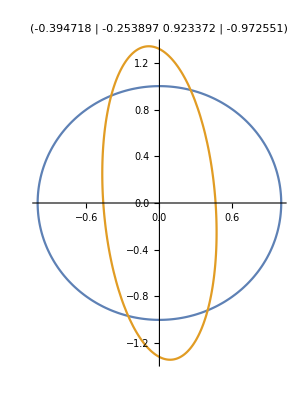

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];
ParametricPlot[{{Cos[θ],Sin[θ]},A.{Cos[θ],Sin[θ]}},{θ,0,2π},PlotRange->All,
PlotLabel->A]
```

### Pictures: ℝ^(3×3)

For any A∈ℝ^(3×3) the image of the unit sphere is an ellipsoid!  The directions and lengths of the axes are clearly of interest!

```mathematica
m=3;
A=RandomReal[{-1,1},{m,m}];
ParametricPlot3D[{
{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]},
A.{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]}
},{θ,0,2π},{ϕ,0,π},PlotRange->All,
Mesh->All]
```

-Graphics3D-

### Pictures: ℝ^(3×2)

For any A∈ℝ^(3×2) the image of the unit circle is an ellipse in 3D!  The directions and lengths of the axes are clearly of interest!

```mathematica
{m,n}={3,2};
A=RandomReal[{-1,1},{m,n}];
ParametricPlot3D[{
A.{Cos[θ],Sin[θ]}
},{θ,0,2π},PlotRange->All,
PlotLabel->A]
```

-Graphics3D-

### Pictures: ℝ^(2×3)

For any A∈ℝ^(2×3) the image of the unit sphere is an ellipse!  The directions and lengths of the axes are clearly of interest!  The ellipse is covered more than once but it is an ellipse.

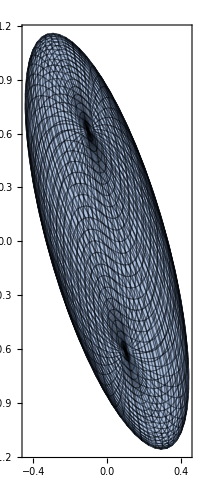

```mathematica
{m,n}={2,3};
A=RandomReal[{-1,1},{m,n}];

ParametricPlot[{
A.{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]}
},{θ,0,2π},{ϕ,0,π},PlotRange->All,
Mesh->All]
```

## SVD: Geometric Interpretation

### SVD: ℝ^(2×2)

The SVD gives us the axes directions and lengths. The column vectors in U are the directions of the axes and the diagonal entries of the diagonal matrix S are the matching lengths.

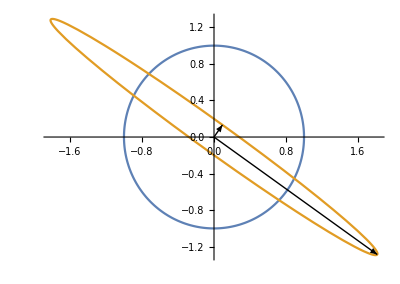

```mathematica
m=2;A=RandomReal[{-2,2},{m,m}];
{U,S,V}=SingularValueDecomposition[A];
{u1,u2}=Uᵀ;{σ1,σ2}=Diagonal[S];
ParametricPlot[{{Cos[θ],Sin[θ]},A.{Cos[θ],Sin[θ]}},{θ,0,2π},PlotRange->All,
Epilog->{{Arrow[{{0,0},σ1 u1}], Arrow[{{0,0},σ2 u2}]}}
]
```

### SVD: ℝ^(3×3)

The SVD gives us the axes directions and lengths. The column vectors in U are the directions of the axes and the diagonal entries of the diagonal matrix S are the matching lengths.

```mathematica
m=3;A=RandomReal[{-1,1},{m,m}];
{U,S,V}=SingularValueDecomposition[A];
{u1,u2,u3}=Uᵀ;{σ1,σ2,σ3}=Diagonal[S];
Show[
ParametricPlot3D[A.{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]},
{θ,0,2π},{ϕ,0,π},PlotRange->All,
PlotStyle->Opacity[0.2]
],
Graphics3D[{Red,Arrow[{{0,0,0},σ1 u1}], 
Arrow[{{0,0,0},σ2 u2}],
Arrow[{{0,0,0},σ3 u3}]}]]
```

-Graphics3D-

### SVD: ℝ^(3×2)

For any A∈ℝ^(3×2) the image of the unit circle is an ellipse in 3D!  The SVD gives the info

```mathematica
{m,n}={3,2};A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A];
{u1,u2,u3}=Uᵀ;
{σ1,σ2}=Diagonal[S];
Show[
ParametricPlot3D[{
A.{Cos[θ],Sin[θ]}
},{θ,0,2π},PlotRange->All],
Graphics3D[{Red,Arrow[{{0,0,0},σ1 u1}], 
Arrow[{{0,0,0},σ2 u2}],
Green,Arrow[{{0,0,0},u3}]}]]
```

-Graphics3D-

### SVD: ℝ^(2×3)

For any A∈ℝ^(2×3) the image of the unit sphere is an ellipse!  The directions and lengths of the axes are clearly of interest!  The ellipse is covered more than once but it is an ellipse.

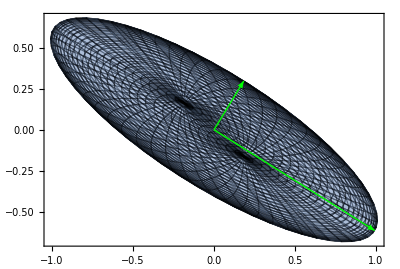

```mathematica
{m,n}={2,3};
A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A];
{u1,u2}=Uᵀ;
{σ1,σ2}=Diagonal[S];
ParametricPlot[{
A.{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]}
},{θ,0,2π},{ϕ,0,π},PlotRange->All,
Mesh->All,
Epilog->{Green,Arrow[{{0,0},σ1 u1}],Arrow[{{0,0},σ2 u2}]}
]
```

## SVD: Algebraic Interpretation

I do not know how to draw pictures in general dimensions!

Algebraically the SVD of A∈ℝ^(m×n) gives 
	A=U.S.Vᵀ
where the columns u_k of the m×m matrix U form an orthogonal basis for the output space ℝ^m and the diagonal of the m×n diagonal matrix S gives axis lengths σ_k of the output m-dimensional hyper-ellipse.  The columns of the n×n orthogonal matrix V  give the input vectors v_k that match u_k in the sense that 
	σ_k u_k=A.v_k
The singular values σ_k (the non-negative diagonals of S) are ordered
	σ_1≥σ_2≥…

```mathematica
τ
```

```mathematica
{m,n}={4,3};
A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A];
Map[Norm,{A-U.S.Vᵀ,Uᵀ.U-IdentityMatrix[m],Vᵀ.V-IdentityMatrix[n]}]
MatrixForm[S]
```

{9.16311×10^-16,9.96493×10^-16,9.15124×10^-16}

(1.76739 | 0. | 0.
0. | 1.47981 | 0.
0. | 0. | 0.80274
0. | 0. | 0.)

## SVD: Thick vs Thin aka Full vs Reduced

A thin SVD drops zero rows and/or columns from the center scaling matrix S and drops the corresponding columns from U and V. In practice, you frequently tell software how many singular values you want (say r) and the software gives you the pieces matching the r biggest singular values!  You now have A≈U.S.Vᵀ but now U and V  are Tall-Skinny matrices. Of course, the columns of U and V are still orthogonal. 

Caution: By default some software gives thin SVDs while some gives thick SVDs.

```mathematica
{m,n,r}={14,10,3};
A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A,r];
Map[Dimensions,{A,U,S,V}]
Map[Norm,{Uᵀ.U-IdentityMatrix[r],Vᵀ.V-IdentityMatrix[r]}]
```

{{14,10},{14,3},{3,3},{10,3}}

{8.42729×10^-16,7.32678×10^-16}

## Rotationally Invariant Matrix Norms from SVD: A=U.S.Vᵀ

If ||A||=||Q_1.A.Q_2|| for all rotations then 
	||A||=||U.S.Vᵀ||=||Uᵀ.U.S.Vᵀ.V||=||S||
So if σ_r>0 and σ_(r+1)=0 the r is the rank of A and 
	||A(||)_F^2=∑_(i=1)^r σ_i^2
and ||A(||)_2=σ_1. Any rotationally invariant matrix norm is determined by the singular values.  There are Schatten and Ky-Fan norms (this is what I would call a Schatten “p” Ky-Fan “k” norm)
	||σ⟦1;;k⟧(||)_p=(∑_(i=1)^k σ_i^p)^(1/p).
These are sufficiently unusual that they do not have a standard notation.  One special case (the Nuclear Norm) does
	||A(||)_*=∑_(i=1)^r σ_i
It is widely used as a proxy for rank!